```mathematica
ClearAll["Global`*"]
```

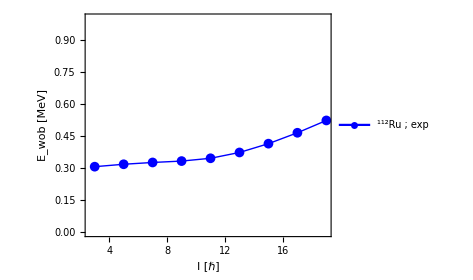

```mathematica
yrastEn=Sort[{7749.3,6725.4,5830.0,4954.6,4118.4,3326.2,2563.0,1839.7,1189.79,644.97,236.69,0.0}];
wob1En=Sort[{6800.4,5857.4,4950.7,4095.4,3290.5,2534.2,1841.1,1235.34,747.48}];
yrastSpin=Table[i,{i,0,22,2}];
wob1Spin=Table[i,{i,3,19,2}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i+1]]+yrast[[i+2]])/1000},{i,1,Length[b1]}];
data=wobbling[yrastEn,wob1En,wob1Spin];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{18,Bold,Black},PlotLegends->Placed[{Row[{Superscript["","112"],"Ru ; exp"}]},{0.3,0.9}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/112Ru.pdf",fig];
Show[fig]
```